# Roche lobes -- analytical discussion

Author : Martin Horvat, November 2015

## Introduction

```mathematica
(* Omega *)
1/rho+q(1/Sqrt[rho^2-2 rho lambda +1]-rho lambda)+1/2(1+q)(1-nu^2) rho^2
```

1/rho+1/2 (1-nu^2) (1+q) rho^2+q (-lambda rho+1/(√(1-2 lambda rho+rho^2)))

```mathematica
(* vector in polar coordinates *)
rho*{Sqrt[1-nu^2]Cos[phi],Sqrt[1-nu^2]*Sin[phi],nu}
```

{√(1-nu^2) rho Cos[phi],√(1-nu^2) rho Sin[phi],nu rho}

## Definiton

```mathematica
Clear[F];
F[{x_,y_,z_},q_]:=Module[
{rho,nu,lambda},
rho=Sqrt[x^2+y^2+z^2];
nu=z/rho;
lambda=x/rho;
1/rho+q(1/Sqrt[rho^2-2 rho lambda +1]-rho lambda)+1/2(1+q)(1-nu^2) rho^2
];

Clear[Fx];
Fx[x_,q_]:=1/Abs[x]+q(1/Abs[x-1]-x)+1/2(1+q)x^2

Clear[P];
P[u_,{x_,w_,q_,q1_}]:=((w-1/2(1+q)(x^2+q1*u)+q x)^2(u+x^2)(u+(x-1)^2)-(u(1+q^2) +(q x)^2+(x-1)^2))^2-(2q)^2(u+x^2)(u+(x-1)^2)

Clear[Pcoef];
Pcoef[{x_,w_,q_,qq_}]=Simplify[
CoefficientList[((w-1/2(1+q)(x^2+qq*u)+q x)^2(u+x^2)(u+(x-1)^2)-(u(1+q^2) +(q x)^2+(x-1)^2))^2-(2q)^2(u+x^2)(u+(x-1)^2),u]];
```

## Some plots

```mathematica
Clear[x,y,z];
```

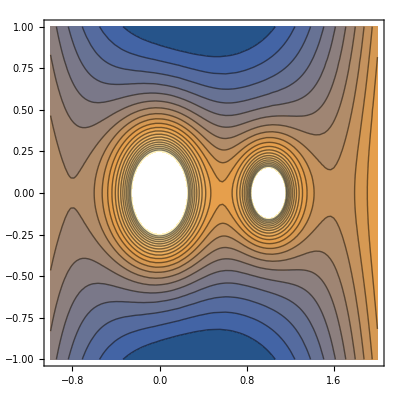

```mathematica
(* in X-Z plane at y = 0 *)
ContourPlot[F[{x,0,z},0.5],{x,-1,2},{z,-1,1},Contours->20]
```

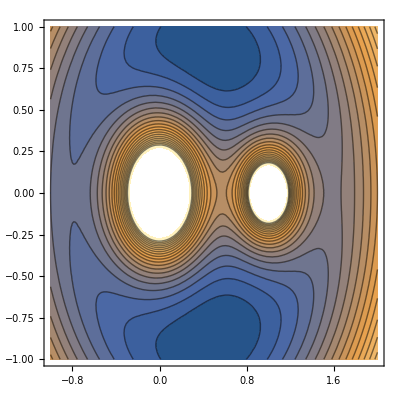

```mathematica
(* in X-Y plane *)
ContourPlot[F[{x,y,0},0.5],{x,-1,2},{y,-1,1},Contours->20]
```

```mathematica
(* on X axis *)
```

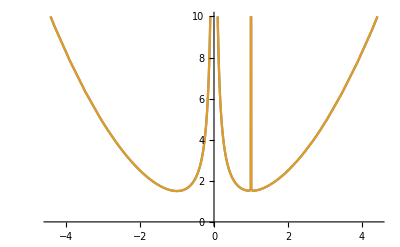

```mathematica
Plot[{F[{x,0,0},1/1000],Fx[x,1/1000]},{x,-10,10},PlotRange->{All,{0,10}}]
```

```mathematica
ContourPlot3D[F[{x,y,z},0.5]==6,{x,-1,2},{y,-2,2},{z,-2,2},PlotPoints->35,PlotRange->All,AxesLabel->{"x","y","z"},AspectRatio->1]
```

-Graphics3D-

There are three critical values of Omega
1. Omega>Omega_(crit,1) : Two indepedent lobes
2. Omega in [Omega_(crit,1),Omega_(crit,2)]: One joined lobes == overcontact case
3. Omega =Omega_(crit,2):Semi-deteched case
4. Omega <Omega_(crit,2): No lobe

## Finding Critical Omegas

### Ideas

```mathematica
Clear[F0,F1,F2,x,q]
(* x<0 *)
F0=-1/x+q(1/(1-x)-x)+1/2(1+q)x^2
Simplify[DF0=D[F0,x]]

(* x>0 and x <1 *)
F1=1/x+q(1/(1-x)-x)+1/2(1+q)x^2
Simplify[DF1=D[F1,x]]

(*x>1*)
F2=1/x+q(1/(x-1)-x)+1/2(1+q)x^2
Simplify[DF2=D[F2,x]]
```

q (1/(1-x)-x)-1/x+1/2 (1+q) x^2

1/x^2+x+q (-1+1/(-1+x)^2+x)

q (1/(1-x)-x)+1/x+1/2 (1+q) x^2

-1/x^2+x+q (-1+1/(-1+x)^2+x)

q (1/(-1+x)-x)+1/x+1/2 (1+q) x^2

-1/x^2+x+q (-1-1/(-1+x)^2+x)

```mathematica
N[x/.Solve[DF0==0,x]/.q->0.1]
```

{-0.946927,0.529816-0.806057 ⅈ,0.529816+0.806057 ⅈ,0.989102-0.231307 ⅈ,0.989102+0.231307 ⅈ}

### Routine

```mathematica
Clear[CriticalOmega]
CriticalOmega[q_]:=Module[{left,center, right,x,F0,DF0,F1,DF1,F2,DF2,res},

F0=-1/x+q(1/(1-x)-x)+1/2(1+q)x^2;
DF0=D[F0,x];

(* x>0 and x <1 *)
F1=1/x+q(1/(1-x)-x)+1/2(1+q)x^2;
DF1=D[F1,x];

(*x>1*)
F2=1/x+q(1/(x-1)-x)+1/2(1+q)x^2;
DF2=D[F2,x];

(* polynomial of 5 order *)
left=Chop[N[x/.NSolve[DF0==0,x]]];
center=Chop[N[x/.NSolve[DF1==0,x]]];
right=Chop[N[x/.NSolve[DF2==0,x]]];

Map[{#,Fx[#,q]}&,
{
First[Select[left,Im[#]==0&&#<0&]],
First[Select[center,Im[#]==0&&0<#<1&]],
First[Select[right,Im[#]==0&&#>1&]]
}
]
];
```

### Calculations

```mathematica
MinOmega=Table[{q,CriticalOmega[q]},{q,1/1000,2,1/1000}];
```

```mathematica
Clear[CriticalOmegaFit];
Do[
CriticalOmegaFit[q_,j]=Fit[
Table[{MinOmega[[i,1]],MinOmega[[i,2,j,2]]},{i,Length[MinOmega]}],
Evaluate[q^(Range[0,6]/6)],q],
{j,3}];
?CriticalOmegaFit
```

Global`CriticalOmegaFit

CriticalOmegaFit[q_,1]=0
 
CriticalOmegaFit[q_,2]=0
 
CriticalOmegaFit[q_,3]=0

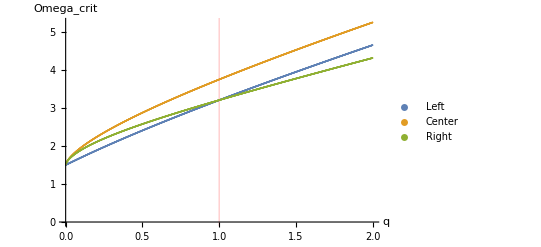

```mathematica
ListPlot[
Table[{MinOmega[[i,1]],MinOmega[[i,2,j,2]]},{j,1,3},{i,Length[MinOmega]}],
PlotRange->All,
GridLines->{{{1,Red}},None},
AxesLabel->{"q","Omega_crit"},PlotLegends->{"Left","Center","Right"}]
```

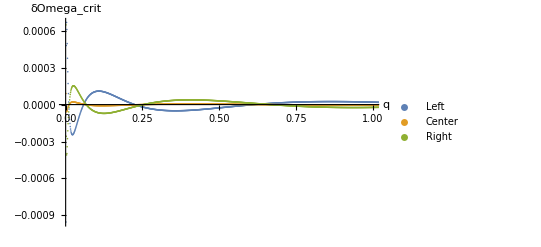

```mathematica
ListPlot[
Table[{MinOmega[[i,1]],(MinOmega[[i,2,j,2]]-CriticalOmegaFit[MinOmega[[i,1]],j])/MinOmega[[i,2,j,2]]},{j,3},{i,Length[MinOmega]}],
PlotRange->{{0,1},All},
AxesLabel->{"q","δOmega_crit"},PlotLegends->{"Left","Center","Right"}]
```

## Nodes

### Routine

```mathematica
Clear[Nodes];
Nodes[q_,Omega_]:=Module[{res,sol,x,DF},

DF[x_]=D[Fx[x,q],x]/.Abs'->Sign;

sol=NSolve[Fx[x,q]==Omega,x];

If [sol!= {},
Map[{#[[1,1]],#[[2,1]]}&,
Select[
Partition[
Map[{#,DF[#]}&,Sort[x/.sol]],
2,1], 
#[[1,2]]>0&&#[[2,2]]<0&
]
]
,
{}]
]
```

### Checking a case

```mathematica
q1=1/10;
OmegaRes1=CriticalOmega[q1]
OmegaCrit1=Sort[OmegaRes1[[All,2]]]
```

{{-0.946927,1.69527},{0.717513,1.9591},{1.34699,1.8938}}

{1.69527,1.8938,1.9591}

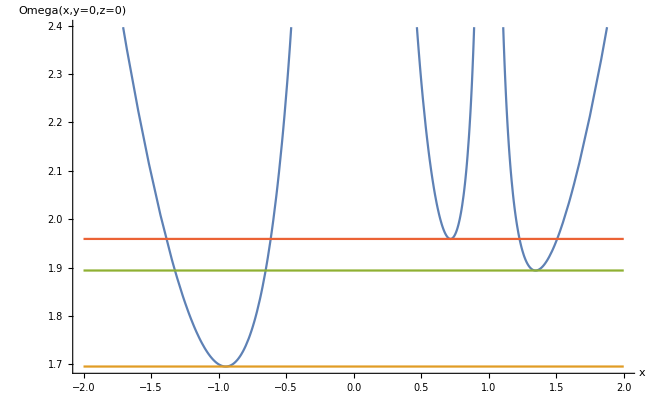

```mathematica
Plot[Evaluate[Join[{Fx[x,q1]},OmegaCrit1]],{x,-2,2},AxesLabel->{"x","Omega(x,y=0,z=0)"}]
```

```mathematica
Print["No lobes=",Nodes[q1,OmegaCrit1[[1]]*0.99]];

Print["No lobes yet=",Nodes[q1,OmegaCrit1[[1]]*1.01]];
Print["No lobes yet=",Nodes[q1,OmegaCrit1[[2]]*0.99]];

Print["Single-lobe=",Nodes[q1,OmegaCrit1[[2]]*1.01]];
Print["Single-lobe=",Nodes[q1,OmegaCrit1[[3]]*0.99]]

Print["Two lobes=",Nodes[q1,OmegaCrit1[[3]]*1.5]]
```

No lobes={}

No lobes yet={}

No lobes yet={}

Single-lobe={{-0.640011,1.27792}}

Single-lobe={{-0.624652,1.24488}}

Two lobes={{-0.362763,0.364329},{0.93249,1.06748}}

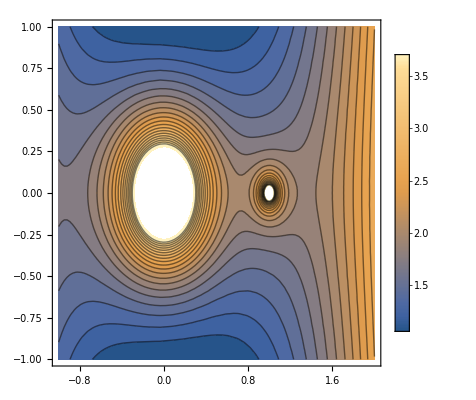

```mathematica
ContourPlot[F[{x,0,z},1/10],{x,-1,2},{z,-1,1},Contours->20,PlotLegends->Automatic]
```

## Lobes the algebraic way/speed up

### Definition

```mathematica
Clear[R,Rpoly];
R[x_,phi_,q_,w_]:=With[{sol=NSolve[{F[{x,r*Cos[phi],r*Sin[phi]},q]== w,r>0}, r,Reals]},If[sol=={},0,Min[r/.sol]]];
Rpoly[x_,phi_,q_,w_]:=
Module[{c,eps=10^-10,u,s},
c=Pcoef[{x,w,q,Cos[phi]^2}];
s=NSolve[{c.u^(Range[Length[c]]-1),u>0},u,Reals];
If[s=={},Return[0]];
s=Select[Sqrt[u/.s],Abs[F[{x,#*Cos[phi],#*Sin[phi]},q]- w]<eps&];
If[s=={},Return[0]];
Min[s]
];
```

### Calculations (2D and 3D)

```mathematica
q1=1/10
OmegaRes1=CriticalOmega[q1]
OmegaCrit1=Sort[OmegaRes1[[All,2]]]
Omega1=OmegaCrit1[[3]]*1.001; (* two lobes almost touching *)
Nodes1=Nodes[q1,Omega1]
```

1/10

{{-0.946927,1.69527},{0.717513,1.9591},{1.34699,1.8938}}

{1.69527,1.8938,1.9591}

{{-0.613118,0.701367},{0.733263,1.22685}}

```mathematica
x1=0.1;
phi=1;
t1=Timing[Rpoly[x1,phi,q1,Omega1]]
t2=Timing[R[x1,phi,q1,Omega1]]
t2[[1]]/t1[[1]]
```

{0.002746,0.53918}

{0.044772,0.53918}

16.3044

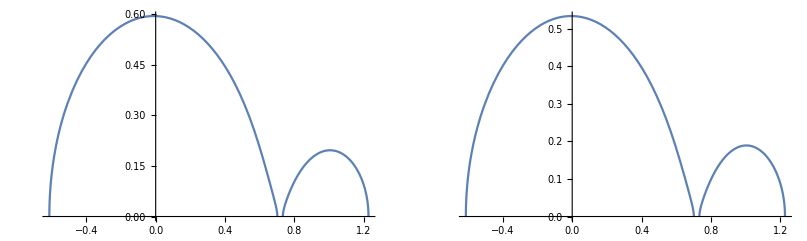

```mathematica
GraphicsGrid[
{{Show[Table[Plot[Rpoly[x,0,q1,Omega1],{x,p[[1]],p[[2]]},PlotRange->All],{p,Nodes1}]],
Show[Table[Plot[R[x,Pi/2,q1,Omega1],{x,p[[1]],p[[2]]},PlotRange->All],{p,Nodes1}]]}}]
```

```mathematica
(* Define the Roche lobe surface *)
Clear[LS];
LS[x_,phi_]:=Rpoly[x,phi,q1,Omega1]*{0,Cos[phi],Sin[phi]}+{x,0,0};
```

```mathematica
Timing[Show[
Table[
ParametricPlot3D[
LS[x,phi],{x,Nodes1[[i,1]],Nodes1[[i,2]]},{phi,0,2Pi},
PlotRange->All,AxesLabel->{"x","y","z"},PlotPoints->{20, 20}],
{i,Length[Nodes1]}]]]
```

{29.496,-Graphics3D-}

## Illumination of lobes without eclipsing

### Definitions

```mathematica
(* Derivatives of the Kopal potential *)
Clear[DOmega];
DOmega=Simplify[D[1/Sqrt[X^2+Y^2+Z^2]+Q(1/Sqrt[X^2+Y^2+Z^2-2 X +1]-X)+1/2(1+Q)(X^2+Y^2),{{X,Y,Z}}]];
DDOmega=Simplify[D[DOmega,{{X,Y,Z}}]];
```

```mathematica
(* Define the Roche lobe surface *)
Clear[LobeSurface];
LobeSurface[x_,phi_,q_,Omega_]:=Rpoly[x,phi,q,Omega]*{0,Cos[phi],Sin[phi]}+{x,0,0};

(* Generate Roche lobes on a grid points  *)
Clear[GenerateSurface];
GenerateSurface[q_,Omega_,{Nx_,Nphi_}]:=Module[{nodes,p, res,surface,vecr,vecn,DS,i,j,k,x,dx,phi, dphi},
nodes=Nodes[q,Omega];

dphi=2Pi/Nphi;
res={};

Do[

(* Chebyshev nodes *)
x=(p[[1]]+p[[2]])/2+(p[[1]]-p[[2]])/2Map[Cos[(2#-1)/(2Nx) Pi]&,Range[Nx]];

vecr={First[x],0,0};
vecn=DOmega/.{Q->q,X->vecr[[1]],Y->vecr[[2]],Z->vecr[[3]]};
surface={{vecr,vecn}};

Do[
phi=0;
Do[
vecr=Rpoly[x[[j]],phi,q,Omega]*{0,Cos[phi],Sin[phi]}+{x[[j]],0,0};
vecn=DOmega/.{Q->q,X->vecr[[1]],Y->vecr[[2]],Z->vecr[[3]]};
AppendTo[surface,{vecr,vecn}];
phi+=dphi,
{k,Nphi}
],
{j,2,Length[x]-1}
];

vecr={Last[x],0,0};
vecn=DOmega/.{Q->q,X->vecr[[1]],Y->vecr[[2]],Z->vecr[[3]]};
AppendTo[surface,{vecr,vecn}];

AppendTo[res,surface],
{p,nodes}];

res
];
```

### Checking surfaces

```mathematica
(* Pole *)
FullSimplify[DOmega/.{X->0,Y->0},Z>0]
FullSimplify[DOmega/.{X->1,Y->0},Z>0]
```

{Q (-1+1/((1+Z^2)^(3/2))),0,-1/Z^2-(Q Z)/((1+Z^2)^(3/2))}

{1-1/((1+Z^2)^(3/2)),0,-Q/Z^2-Z/((1+Z^2)^(3/2))}

```mathematica
q1=1/10;
OmegaCrit1=Sort[CriticalOmega[q1][[All,2]]] ;(* Critical omega values for q1*)
Omega1=OmegaCrit1[[3]]*0.97; (* two lobes almost touching *)
Nodes1=Nodes[q1,Omega1]

light1={1,1,1};
light=light1/Norm[light1];
```

{{-0.647568,1.30495}}

```mathematica
(* Generate mash of points laying the lobes *)
data=GenerateSurface[q1,Omega1,{200,200}];
```

```mathematica
(* nf=Table[Nearest[data[[i,All,1]]->UnitStep[data[[i,All,2]].light]],{i,Length[data]}];*)
nf=Table[UnitStep[(DOmega/.{Q->q1,X->#1,Y->#2,Z->#3}).light]&,{i,Length[data]}];
colorfun=Table[GrayLevel@nf[[i]][#1,#2,#3]&,{i,Length[data]}];
```

```mathematica
(* Using native mathematica Parametric plot *)
Nodes1=Nodes[q1,Omega1];
Show[
Table[
ParametricPlot3D[
LobeSurface[x,phi,q1,Omega1],{x,Nodes1[[i,1]],Nodes1[[i,2]]},
{phi,0,2Pi},
PlotRange->All,
AxesLabel->{"x","y","z"},
ColorFunction->colorfun[[i]],
ColorFunctionScaling->False,
PlotPoints->{50, 50}],
{i,Length[Nodes1]}]]
```

-Graphics3D-

```mathematica
(* Simple  ListSurfacePlot3D *)
Show@@Table[ListSurfacePlot3D[First/@d,PlotRange->All,AxesLabel->{"x","y","z"},MaxPlotPoints->50],{d,data}]
```

-Graphics3D-

```mathematica
(* ListSurfacePlot3D with capturing direction of the normal *)
Show@@Table[
ListSurfacePlot3D[First/@data[[i]],
PlotRange->All,
AxesLabel->{"x","y","z"},
ColorFunction->colorfun[[i]],
ColorFunctionScaling->False,
MaxPlotPoints->100],
{i,Length[data]}]
```

-Graphics3D-

```mathematica
(* Just data points *)
dataP=Flatten[Table[First/@Select[d,#[[2]].light>0&],{d,data}],1];
dataN=Flatten[Table[First/@Select[d,#[[2]].light<0&],{d,data}],1];
```

```mathematica
ListPointPlot3D[{dataP,dataN},PlotRange->All,PlotStyle->{Red,Blue}]
```

-Graphics3D-

## Horizon without eclipsing

### Definition

```mathematica
(* Derivative of the curve along the horizon *)
Clear[HorizonDerivative];
HorizonDerivative[r_,p_,q_]:=Module[{H,V,U},
H=(DDOmega/.{Q->q,X->r[[1]],Y->r[[2]],Z->r[[3]]}).p;
V=DOmega/.{Q->q,X->r[[1]],Y->r[[2]],Z->r[[3]]};
U=Cross[H,V];

U/Norm[U]
];

(* Plotting the surface over (x, phi) in [xmin,xmax] x [0,2Pi] *)
Clear[PlotPointHorizon];
PlotPointHorizon[{xmin_,xmax_},p_,q_,Omega_]:=Module[{pos,normal,x,phi},

pos[x_,phi_]:=LobeSurface[x,phi,q,Omega];
normal[{x_,y_,z_}]=DOmega/.{Q->q,X->x,Y->y,Z->z};

Plot3D[
normal[pos[x,phi]].p,{x,xmin,xmax},{phi,0,2Pi},
ColorFunction->Function[{x,y,z},GrayLevel[UnitStep[z]]],
ColorFunctionScaling->False,
PlotPoints->50,
AxesLabel->{"x","phi","normal.p"}
]
];

(* Plotting the surface at given x *)
PlotPointHorizon[x_,p_,q_,Omega_]:=Module[{pos,normal,phi,xave,x1,y1,z1},

pos[phi_]:=LobeSurface[x,phi,q,Omega];
normal[{x1_,y1_,z1_}]=DOmega/.{Q->q,X->x1,Y->y1,Z->z1};

Plot[normal[pos[phi]].p,{phi,0,2Pi},AxesLabel->{"phi","normal.p"}]
];

(* Bisection for finding zeros *)
Clear[Bisection];
Bisection[f_,{a_,b_},eps_]:=Module[{c,d,e},

{c,d}=If[f[a]>0,{b,a},{a,b}];

While[d-c>eps,
e=(c+d)/2;
If[f[e]<0,c=e,d=e];
];

(c+d)/2
];

(* Bisection like searching for minimum *)
Clear[MyFindMinimum];
MyFindMinimum[f_,x_,a_]:=MyFindMinimum[f,x,a,0];
MyFindMinimum[f_,x_,a_,n_]:=Module[{x0,a0,x1,a1,fmin,X,A,s},

fmin=a[[2]];

If[n>256||fmin==0||(Max[x]-Min[x]<10^-8) || (Max[a]-Min[a]<10^-14), 
Return[{x[[2]],a[[2]]}]
];

x0=(x[[1]]+x[[2]])/2;
a0=f[x0];

If[a0<fmin,
X={x[[1]],x0,x[[2]]};
A={a[[1]],a0,a[[2]]};
s=MyFindMinimum[f,X,A,n+1]
,
x1=(x[[2]]+x[[3]])/2;
a1=f[x1];

If[a1<fmin,
X={x[[2]],x1,x[[3]]};
A={a[[2]],a1,a[[3]]};
s=MyFindMinimum[f,X,A,n+1]
,
X=x;
A=a;

If[a0<A[[1]],
X[[1]]=x0;
A[[1]]=a0;
];

If[a1<A[[3]],
X[[3]]=x1;
A[[3]]=a1;
];
s=MyFindMinimum[f,X,A,n+1]
];
];
s
];

(* Finding one point on the horizon at a given x *)
Clear[FindPointHorizon];
FindPointHorizon[x_,p_,q_,Omega_]:=Module[{pos,t1,t2,normal,phi,phi1,dphi,sol,x1,y1,z1},

pos[phi_]:=LobeSurface[x,phi,q,Omega];
normal[{x1_,y1_,z1_}]=DOmega/.{Q->q,X->x1,Y->y1,Z->z1};

phi=0;
dphi=2Pi/100;
t1=normal[pos[phi]].p;

sol={};
While[phi < 2Pi,
t2=t1;
phi+=dphi;
t1=normal[pos[phi]].p;
If[t1*t2<0,
sol=Bisection[normal[pos[#]].p&,{phi-dphi,phi},10^-16];
Break[]
]
];
sol
];

Clear[LengthHorizon];
LengthHorizon[r_,p_,q_]:=Module[{s,c,sol,h,x,y,z,smax,ds,eps=0.01,nmax=10^4,f,v},

smax=20;

h=NDSolveValue[{
{x'[s],y'[s],z'[s]}==HorizonDerivative[{x[s],y[s],z[s]},p,q],
{x[0],y[0],z[0]}==r
},
{x,y,z},
{s,0,smax}];


f[s_]:=Norm[#[s]&/@h-r];

ds=smax/nmax;
v=Map[f,{ds,2*ds}];
s=3*ds;

sol={};
While[s≤smax,

AppendTo[v,f[s]];

If[(v[[1]]>v[[2]]<v[[3]])&&(v[[2]]<eps),
sol=MyFindMinimum[f,{s-2ds,s-ds,s},v];
Break[];
];
v=Rest[v];
s+=ds;
];
sol[[1]]
];
```

```mathematica
??PlotPointHorizon
```

Global`PlotPointHorizon

PlotPointHorizon[{xmin_,xmax_},p_,q_,Omega_]:=Module[{pos,normal,x,phi},pos[x_,phi_]:=LobeSurface[x,phi,q,Omega];normal[{x_,y_,z_}]=DOmega/.{Q→q,X→x,Y→y,Z→z};Plot3D[normal[pos[x,phi]].p,{x,xmin,xmax},{phi,0,2 π},ColorFunction→Function[{x,y,z},GrayLevel[UnitStep[z]]],ColorFunctionScaling→False,PlotPoints→50,AxesLabel→{x,phi,normal.p}]]
 
PlotPointHorizon[x_,p_,q_,Omega_]:=Module[{pos,normal,phi,xave,x1,y1,z1},pos[phi_]:=LobeSurface[x,phi,q,Omega];normal[{x1_,y1_,z1_}]=DOmega/.{Q→q,X→x1,Y→y1,Z→z1};Plot[normal[pos[phi]].p,{phi,0,2 π},AxesLabel→{phi,normal.p}]]

### Finding the point on a horizon for a specific case

```mathematica
q1=1/10;
OmegaCrit1=Sort[CriticalOmega[q1][[All,2]]] ;(* Critical omega values for q1*)
Omega1=OmegaCrit1[[3]]*0.97; (* two lobes almost touching *)
Nodes1=Nodes[q1,Omega1]
```

{{-0.647568,1.30495}}

```mathematica
light1={1,1,1};
light=light1/Norm[light1];
```

```mathematica
PlotPointHorizon[Nodes1[[1]],light1,q1,Omega1]
```

-Graphics3D-

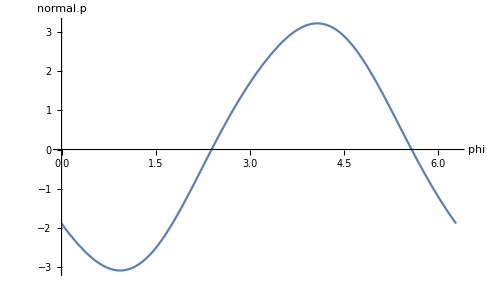

```mathematica
PlotPointHorizon[1.0,light1,q1,Omega1]
```

```mathematica
x1=1;
phi1=N[FindPointHorizon[x1,light1,q1,Omega1]]
r1=LobeSurface[x1,phi1,q1,Omega1]
```

2.38913

{1.,-0.15893,0.148791}

### Calculating the horizon

```mathematica
len1=N[LengthHorizon[r1,light,q1]]
```

5.54969

```mathematica
horizon1=NDSolveValue[{
{x'[s],y'[s],z'[s]}==HorizonDerivative[{x[s],y[s],z[s]},light,q1],
{x[0],y[0],z[0]}==r1
},
{x,y,z},
{s,0,1.1*len1}]
```

{InterpolatingFunction[{{0., 6.10466}}, <>],InterpolatingFunction[{{0., 6.10466}}, <>],InterpolatingFunction[{{0., 6.10466}}, <>]}

```mathematica
(* Generate mash of points laying the lobes *)
data=GenerateSurface[q1,Omega1,{200,200}];
```

```mathematica
(* Just data points *)
dataP=Flatten[Table[First/@Select[d,#[[2]].light>0&],{d,data}],1];
dataN=Flatten[Table[First/@Select[d,#[[2]].light<0&],{d,data}],1];
```

```mathematica
Show[
ListPointPlot3D[{dataP,dataN,{r1}},PlotRange->All,PlotStyle->{{PointSize[Tiny],Red},{PointSize[Tiny],Blue},{PointSize[Medium],Black}}],
ParametricPlot3D[{horizon1[[1]][t],horizon1[[2]][t],horizon1[[3]][t]},{t,0,len1},PlotStyle->{Thick,Black}]
]
```

-Graphics3D-

## Lobes with eclipsing

```mathematica
q1=1/10;
OmegaCrit1=Sort[CriticalOmega[q1][[All,2]]] ;(* Critical omega values for q1*)
Omega1=OmegaCrit1[[3]]*0.97; (* two lobes almost touching *)
Nodes1=Nodes[q1,Omega1]

(* Generate mash of points laying the lobes *)
data=GenerateSurface[q1,Omega1,{200,200}];
```

{{-0.647568,1.30495}}

```mathematica
light1={1,1,1};
light=light1/Norm[light1];
```

```mathematica
(* Just data points *)
dataP=Flatten[Table[First/@Select[d,#[[2]].light>0&],{d,data}],1];
dataN=Flatten[Table[First/@Select[d,#[[2]].light<0&],{d,data}],1];
```

```mathematica
ListPointPlot3D[{dataP,dataN},PlotRange->All,PlotStyle->{{PointSize[Tiny],Red},{PointSize[Tiny],Blue}}]
```

-Graphics3D-